## QCD Phase Transition with explicit symmetry breaking

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
ProgressBar[dynvar_,varp_,varm_]:=Row[{ProgressIndicator[N[Dynamic[(dynvar-varm)/(varp-varm)]],{0,1}],Dynamic[N[(dynvar-varm)/(varp-varm) 100]] ,"%"}," "]
```

```mathematica
(*Constants, all energies in Gev*)
Nc=3;
Nf=2;
Ns=2;
Deg=Ns Nc Nf;
mq=0.335;
msig=0.570;
mpi=0.138;
fpi=0.093;
Lam=10;(*=infinity, results mostly independent for Lam>>msig*)
g=mq/fpi;
M=0.5;
eps0=fpi mpi^2;
```

```mathematica
lam[eps_]:=(3*Deg*fpi^3*g^4-8*(eps-fpi*msig^2)*Pi^2+4*Deg*fpi^3*g^4*Log[(fpi*g)/M])/(16*fpi^3*Pi^2)
V2[eps_]:=(2*fpi^2*(Deg*fpi^3*g^4+4*(-3*eps+fpi*msig^2)*Pi^2))/(3*Deg*fpi^3*g^4-8*(eps-fpi*msig^2)*Pi^2+4*Deg*fpi^3*g^4*Log[(fpi*g)/M])
```

```mathematica
eps0
lam[eps0]
V2[eps0]
```

0.00177109

35.5688

0.00998615

```mathematica
(*Energy in dependence on sig and P*)
En[p_,sig_]:=Sqrt[p^2+g^2 sig^2];
```

```mathematica
(*Fermionic pressure*)
int[sig_,T_,mu_]:=p^2(T Log[1+Exp[(mu-En[p,sig])/T]]+T Log[1+Exp[-(mu+En[p,sig])/T]])
vac[sig_]:=Deg/(16 Pi^2) g^4sig^4 Log[sig g/M]
PF[sig_,T_,mu_]:=vac[sig]+Deg/(2Pi^2)NIntegrate[int[sig,T,mu],{p,0,Lam}]
(*Bosonic pressure*)
PB[sig_,eps_]:=-lam[eps]/4(sig^2-V2[eps])^2+eps sig
(*Altogether*)
Pa[sig_,eps_,T_,mu_]:=PF[sig,T,mu]+PB[sig,eps]
```

```mathematica
(*Derivatives in respect to sig*)
vac1[sig_]=D[vac[sigs],{sigs,1}]/.sigs->sig//Simplify;
vac2[sig_]=D[vac[sigs],{sigs,2}]/.sigs->sig//Simplify;
vac3[sig_]=D[vac[sigs],{sigs,3}]/.sigs->sig//Simplify;
vac4[sig_]=D[vac[sigs],{sigs,4}]/.sigs->sig//Simplify;
int1[sig_,T_,mu_]=D[int[sigs,T,mu],{sigs,1}]/.sigs->sig;
int2[sig_,T_,mu_]=D[int[sigs,T,mu],{sigs,2}]/.sigs->sig;
int3[sig_,T_,mu_]=D[int[sigs,T,mu],{sigs,3}]/.sigs->sig;
int4[sig_,T_,mu_]=D[int[sigs,T,mu],{sigs,4}]/.sigs->sig;
PB1[sig_,eps_]=D[PB[sigs,eps],{sigs,1}]/.sigs->sig//Simplify;
PB2[sig_,eps_]=D[PB[sigs,eps],{sigs,2}]/.sigs->sig//Simplify;
PB3[sig_,eps_]=D[PB[sigs,eps],{sigs,3}]/.sigs->sig//Simplify;
PB4[sig_,eps_]=D[PB[sigs,eps],{sigs,4}]/.sigs->sig//Simplify;
Pder1[sig_,eps_,T_,mu_]:=vac1[sig]+Deg/(2Pi^2)NIntegrate[int1[sig,T,mu],{p,0,Lam}]+PB1[sig,eps]
Pder2[sig_,eps_,T_,mu_]:=vac2[sig]+Deg/(2Pi^2)NIntegrate[int2[sig,T,mu],{p,0,Lam}]+PB2[sig,eps]
Pder3[sig_,eps_,T_,mu_]:=vac3[sig]+Deg/(2Pi^2)NIntegrate[int3[sig,T,mu],{p,0,Lam}]+PB3[sig,eps]
Pder4[sig_,eps_,T_,mu_]:=vac4[sig]+Deg/(2Pi^2)NIntegrate[int4[sig,T,mu],{p,0,Lam}]+PB4[sig,eps]
```

```mathematica
(*Derivatives in respect to mu (baryon number susceptibility)*)
int1mu[sig_,T_,mu_]=D[int[sig,T,mus],{mus,1}]/.mus->mu;
int2mu[sig_,T_,mu_]=D[int[sig,T,mus],{mus,2}]/.mus->mu;
Pder1mu[sig_,eps_,T_,mu_]:=Deg/(2Pi^2)NIntegrate[int1mu[sig,T,mu],{p,0,Lam}]
Pder2mu[sig_,eps_,T_,mu_]:=Deg/(2Pi^2)NIntegrate[int2mu[sig,T,mu],{p,0,Lam}]
```

```mathematica
(*Mixed derivatives in respect to mu and sig*)
int2musig[sig_,T_,mu_]=D[int1mu[sigs,T,mu],{sigs,1}]/.sigs->sig;
int2sigmu[sig_,T_,mu_]=D[int1[sig,T,mus],{mus,1}]/.mus->mu;
Pder2sigmu[sig_,eps_,T_,mu_]:=Deg/(2Pi^2)NIntegrate[int2sigmu[sig,T,mu],{p,0,Lam}]
```

```mathematica
(*The maximum for T=0 and mu=0 must be at sig=fpi*)
sig/.FindRoot[Pder1[sig,eps0,0.005,0]==0,{sig,0.1}]//Quiet
```

0.093

```mathematica
(*Limits*)
steplow=10;
mum=0;mup=0.4;Tm=0.005;Tp=0.20;step=200;sig0=0.00001;
(*Helper functions*)
(*get a real number for a given integer representing mu, or get an integer number for a given real mu*)
muQ[muN_]:=mum+(muN-1)*(mup-mum)/step
muI[muQ_]:=IntegerPart[(muQ-mum)/(mup-mum)step+1]
(*Same for temperature*)
TQ[TN_]:=Tm+(TN-1)*(Tp-Tm)/step
TI[TQ_]:=IntegerPart[(TQ-Tm)/(Tp-Tm)step+1]
```

```mathematica
(*Find the critical end point (CEP)*)
repl[eps_]:=FindRoot[{Pder1[sig,eps,T,mu]==0,Pder2[sig,eps,T,mu]==0,Pder3[sig,eps,T,mu]==0},{{sig,0.08},{T,0.06},{mu,0.33}}]//Quiet
repl0=repl[eps0];
sigCEP=sig/.repl0
TCEP=T/.repl0
muCEP=mu/.repl0
```

0.0538325

0.0418454

0.315684

```mathematica
(*Create a table to determine the eps dependency of sig at the CEP -> to determine c in landau model -> Susceptibilities*)
(*epsm=0;
epsp=0.002;
sigCEPTable=Table[{eps,sig/.repl[eps]},{eps,epsm,epsp,(epsp-epsm)/100}];
Export["sigCEPTable.wdx",sigCEPTable,"WDX"];*)
```

```mathematica
(*test the results*)
Pder1[sigCEP,eps0,TCEP,muCEP]
Pder2[sigCEP,eps0,TCEP,muCEP]
Pder3[sigCEP,eps0,TCEP,muCEP]
```

1.73472×10^-18

-2.77556×10^-17

-2.66454×10^-14

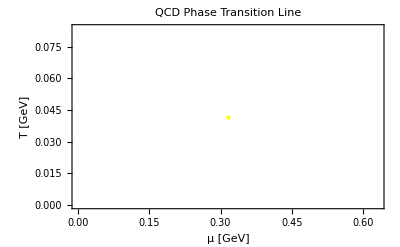

```mathematica
(*plot critical end point*)
plotCEP=ListPlot[{{muCEP,TCEP}},PlotStyle->Directive[PointSize[Large],Yellow],FrameLabel->{"μ [GeV]","T [GeV]"},
LabelStyle->{FontSize->18},
PlotLabel->Text[Style["QCD Phase Transition Line",FontSize->18]],Frame->True]
```

```mathematica
(*Determine the position of the pressure maxima (sigstar) in dependence on T and mu*)
root1[eps_,T_,mu_]:=sig/.FindRoot[Pder1[sig,eps,T,mu]==0,{sig,0.1}]
root2[eps_,T_,mu_]:=sig/.FindRoot[Pder1[sig,eps,T,mu]==0,{sig,0.001}]
sigstar[eps_,T_,mu_]:=Re[If[Re[Pa[(sig1=root1[eps,T,mu]),eps,T,mu]]>Re[Pa[(sig2=root2[eps,T,mu]),eps,T,mu]],sig1,sig2]]//Quiet
```

```mathematica
(*test*)
sigstar[eps0,0.05,0.4]
```

0.0057605

```mathematica
(*generate the table*)
(*tabsigstar200=Table[{mu,T,sigstar[eps0,T,mu]},{mu,mum,mup,(mup-mum)/step},{T,Tm,Tp,(Tp-Tm)/step}];
Export["tabsigstar200_esb.wdx",tabsigstar200,"WDX"];*)
```

```mathematica
tabsigstar=Import["tabsigstar200_esb.wdx"];
```

```mathematica
(*(ColorData[{"LightTemperatureMap","Reverse"}])*)
(*densityPlotSig=ListDensityPlot[Flatten[tabsigstar,1],FrameLabel->{"μ [GeV]","T [GeV]"},ColorFunction->"LightTemperatureMap",LabelStyle->{FontSize->18},PlotLabel->Text[Style["QCD Phase Diagram",FontSize->18]]];
Export["densityPlotSig_esb.wdx",densityPlotSig,"WDX"];*)
```

```mathematica
densityPlotSigImp=Import["densityPlotSig_esb.wdx"]
```

-Graphics-

```mathematica
(*Calculate the crossover line*)
(*Suszeptibility, calculated with the differential coefficient*)
h=0.000001;
Chi[eps_,T_,mu_]:=Re[(sigstar[eps+h,T,mu]-sigstar[eps,T,mu])/h]//Quiet
Chilist[eps_,mu_]:=Table[{T,Chi[eps,T,mu]},{T,TCEP,Tp,(Tp-Tm)/step}];
```

```mathematica
(*Other Solution (better!)*)
chi[eps_,T_,mu_]:=-Re[(Pder2[sigstar[eps,T,mu],eps,T,mu])^(-1)]
chilist[eps_,mu_]:=Table[{T,chi[eps,T,mu]},{T,TCEP,Tp,(Tp-Tm)/step}];
```

```mathematica
(*Export["ChiralSusc1_esb.wdx",Chilist[eps0,0],"WDX"];
Export["ChiralSusc2_esb.wdx",chilist[eps0,0],"WDX"];*)
```

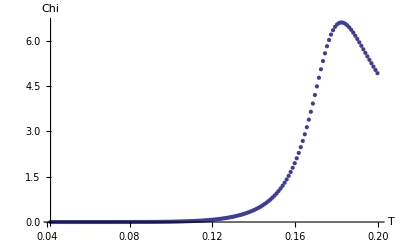

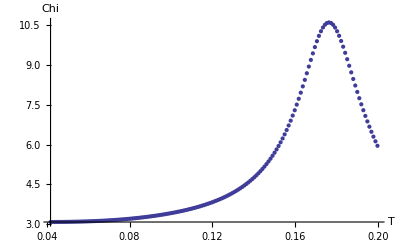

```mathematica
ChiList1=Import["ChiralSusc1_esb.wdx"];
ChiList2=Import["ChiralSusc2_esb.wdx"];
ListPlot[ChiList1,AxesLabel->{"T","Chi"}]
ListPlot[ChiList2,AxesLabel->{"T","Chi"}]
```

```mathematica
(*Cross over temperature in dependence on mu*)
(*TCrO[eps_,mu_]:=(list=Chilist[eps,mu])[[Position[list,Max[list]][[1,1]]]][[1]]
TCrOlist200=Table[{mu,TCrO[eps0,mu]},{mu,mum,muCEP,(mup-mum)/step}];
Export["TCrOlist200_esb.wdx",TCrOlist200,"WDX"];*)
```

```mathematica
(*Cross over temperature in dependence on mu, other solution*)
(*TCrO[eps_,mu_]:=(list=chilist[eps,mu])[[Position[list,Max[list]][[1,1]]]][[1]]
TCrOlist200=Table[{mu,TCrO[eps0,mu]},{mu,mum,muCEP,(mup-mum)/step}];
Export["TCrOlist200_esb_oth.wdx",TCrOlist200,"WDX"];*)
```

```mathematica
TCrOlist=Import["TCrOlist200_esb.wdx"];
 TCrOlistOth=Import["TCrOlist200_esb_oth.wdx"];
```

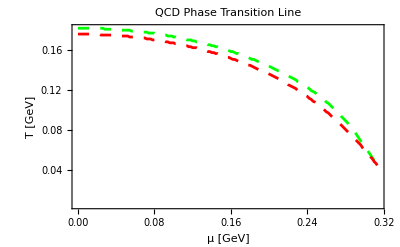

```mathematica
Show[plotCrossOver=ListPlot[TCrOlist,AxesLabel->{"mu","T"},Joined->True,PlotStyle->{Dashing[0.02],Green,Thickness[0.005]},AxesOrigin->{mum,Tm},FrameLabel->{"μ [GeV]","T [GeV]"},
LabelStyle->{FontSize->18},
PlotLabel->Text[Style["QCD Phase Transition Line",FontSize->18]],Frame->True],
plotCrossOverOth=ListPlot[TCrOlistOth,AxesLabel->{"mu","T"},Joined->True,PlotStyle->{Dashing[0.02],Red,Thickness[0.005]},AxesOrigin->{mum,Tm},FrameLabel->{"μ [GeV]","T [GeV]"},
LabelStyle->{FontSize->18},
PlotLabel->Text[Style["QCD Phase Transition Line",FontSize->18]],Frame->True]]
```

```mathematica
(*phase border for the 1st order transition*)
(*threshold=-3*10^(-5);
fn[muN_,TN_]:=-Abs[Pa[sig0,eps0,TQ[TN],muQ[muN]]-Pa[tabsigstar[[muN]][[TN]][[3]],eps0,TQ[TN],muQ[muN]]]
fnlist[muN_]:=Table[fn[muN,TN],{TN,1,step}]
positionZero[muN_]:=Flatten[Position[fnlist[muN],Select[fnlist[muN],#≥threshold&,1][[1]]],2][[1]]
Tc1stlist200=Table[{muQ[muN],TQ[positionZero[muN]]},{muN,muI[muCEP]+1,muI[0.336]-1}];
Export["Tc1stlist200_esb.wdx",Tc1stlist200,"WDX"];*)
```

```mathematica
Tc1stlist=Import["Tc1stlist200_esb.wdx"];
```

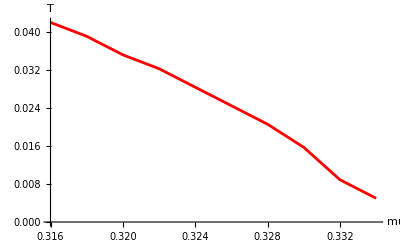

```mathematica
plotTc1st=ListPlot[Tc1stlist,AxesLabel->{"mu","T"},Joined->True,PlotStyle->{Red,Thickness[0.005]}]
```

```mathematica
(*Plot overall phase diagram*)
text=Show[Graphics[{Yellow,FontSize->18,Text["CEP",{muCEP+0.02,TCEP}]}],Graphics[{Yellow,FontSize->18,Text["crossover",{muCEP-0.025,TCEP+0.08}]}],Graphics[{Yellow,FontSize->18,Text["1st",{muCEP+0.03,TCEP-0.02}]}],Graphics[{White,FontSize->18,Text["(b)",{0.36,0.18}]}]];
lines=Show[plotCrossOverOth,plotTc1st,plotCEP,PlotRange->{{mum,mup},{Tm,Tp}},AxesOrigin->{mum,Tm},ImageSize->{600,400}];
Export["PhaseTransitionLine_esb.wdx",lines,"WDX"];
PhaseTransitionDensity=Show[{densityPlotSigImp,plotCrossOverOth,plotTc1st,plotCEP,text},PlotRange->{{mum,mup},{Tm,Tp}},AxesOrigin->{mum,Tm},ImageSize->{500,500}]
Export["PhaseTransitionDensity_esb.wdx",PhaseTransitionDensity,"WDX"];
Export["PhaseTransitionDensity_esb.pdf",PhaseTransitionDensity,"PDF"];
```

-Graphics-

## Baryon Number Susceptibility on lines going through CEP

```mathematica
(*The scaling coefficient will be important around t=0, so choose for the fit only points in a narrow region around t=0*)
choose=-20;(*choose=All*)
```

```mathematica
Clear[sigs]
```

```mathematica
(*Baryon number susceptibility in respect to sig, eps, T, mu*)
chiB[eps_,T_,mu_]:=Pder2mu[sigs=sigstar[eps,T,mu],eps,T,mu]-Pder2sigmu[sigs,eps,T,mu]^2(Pder2[sigs,eps,T,mu])^(-1)
```

```mathematica
chiB[eps0,TCEP+0.1,muCEP]
Clear[sigs]
chiB[eps0,TCEP,muCEP]
chiB[eps0,TCEP+0.1,muCEP]
```

0.101412

$Aborted

0.101412

```mathematica
(*Density plot of the baryon number susc. for h=0*)
(*step=10;
ProgressBar[mu,mup,mum]
ProgressBar[T,Tp,Tm]
chiBlist=Flatten[Table[{mu,T,Re[chiB[eps0,T,mu]]},{T,Tm,Tp,(Tp-Tm)/step},{mu,mum,mup,(mup-mum)/step}],1]//Quiet;
Export["chiBlist_esb.wdx",chiBlist,"WDX"];*)
```

```mathematica
chiBlist=Import["chiBlist_esb.wdx"];
```

```mathematica
LogarithmicScaling[x_,min_,max_]:=Log[x/min]/Log[max/min]
plotter[min_,max_,NumberOfTicks_]:=ListDensityPlot[Re[chiBlist],PlotRange->Full,ColorFunctionScaling->False,ColorFunction->(ColorData["LightTemperatureMap"][LogarithmicScaling[#,min,max]]&),FrameLabel->{"μ [GeV]","T [GeV]"},LabelStyle->{FontSize->16},PlotLabel->Text[Style["Baryon number susceptibility for h = ϵ_0",FontSize->16]],ImageSize->{400,400},PlotLegends->BarLegend[{ColorData["LightTemperatureMap"],{0,1}},LegendMarkerSize->370,Ticks->({LogarithmicScaling[#,min,max],ScientificForm[#,2]}&/@(min (max/min)^Range[0,1,1/NumberOfTicks])),LabelStyle->{FontSize->16}]]
```

```mathematica
(*logdensityPlotChiB=plotter[0.001,100,5]
logdensityPlotChiBRasterized=Rasterize[logdensityPlotChiB,RasterSize->1000];
Export["chiBLogPlot_esb.wdx",logdensityPlotChiBRasterized,"WDX"];
Export["chiBLogPlot_esb.pdf",logdensityPlotChiBRasterized,"PDF"];*)
```

```mathematica
logdensityPlotChiBRasterized=Import["chiBLogPlot_esb.wdx"]
```

-Graphics-

### Baryon number susceptibility on the line μ=μ_CEP

```mathematica
(*Baryon number Susceptibility near the CEP for eps=0 and μ=Subscript[μ, CEP]*)
(*step=400;
ProgressBar[T,1.5TCEP,Tm]
chiBlisth0muCEP=Table[{(T-TCEP)/TCEP,Re[chiB[eps0,T,muCEP]]},{T,Tm,1.5TCEP,(1.5TCEP-Tm)/step}];
Export["chiBlisth0_muCEP_esb.wdx",chiBlisth0muCEP,"WDX"];*)
```

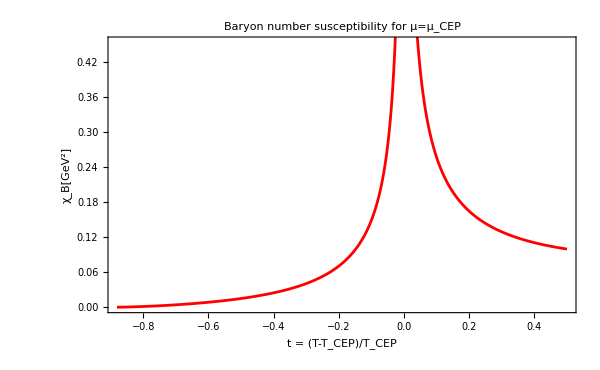

```mathematica
(*Plot the results for mu=muCEP*)
chiBlisth0muCEP=Import["chiBlisth0_muCEP_esb.wdx"];
plot=ListPlot[{chiBlisth0muCEP},FrameLabel->{"t = (T-T_CEP)/T_CEP","χ_B[GeV^2]"},LabelStyle->{FontSize->16},Joined->True,Frame->True,PlotLabel->Style["Baryon number susceptibility for μ=μ_CEP",FontSize->18],ImageSize->{600,400},PlotStyle->{Directive[Red,AbsoluteThickness[2]]},AxesOrigin->{-0.8,0}]
Export["chiBlisth0_muCEP_esb.pdf",plot,"PDF"];
```

```mathematica
(*Fit the susc. for t<0 to determine the scaling coefficient β*)
step=400;
model=α t^(-β);
fit0muCEP=FindFit[Abs[Take[Take[chiBlisth0muCEP,256],-5]],model,{α,β},t]
```

{α→0.039795,β→0.694921}

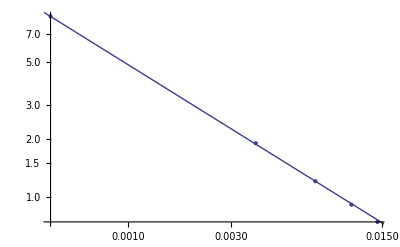

```mathematica
(*Test the fit. Note that the x-axis is now inverted and positive*)
Show[{ListLogLogPlot[{Abs[Take[Take[chiBlisth0muCEP,256],-5]]}],LogLogPlot[{model/.fit0muCEP},{t,0.0002,-(Tm-TCEP)/TCEP}]}]
```

### Baryon number susceptibility on the line T=T_CEP

```mathematica
(*Baryon number Susceptibility near the CEP for eps=h0 and T=Subscript[T, CEP]*)
step=400;
ProgressBar[mu,mup,mum]
chiBlisth0TCEP=Table[{(mu-muCEP)/muCEP,chiB[eps0,TCEP,mu]},{mu,mum,mup,(mup-mum)/step}]//Quiet;
Export["chiBlisth0_TCEP_esb.wdx",chiBlisth0TCEP,"WDX"];
```

%

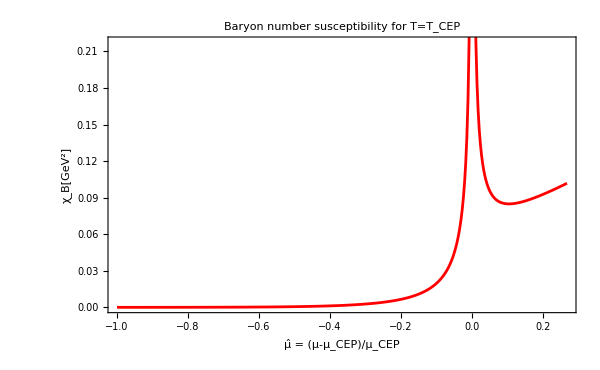

```mathematica
(*Plot the results for mu=muCEP*)
chiBlisth0TCEP=Import["chiBlisth0_TCEP_esb.wdx"];
plot=ListPlot[{chiBlisth0TCEP},FrameLabel->{"μ̂ = (μ-μ_CEP)/μ_CEP","χ_B[GeV^2]"},LabelStyle->{FontSize->16},Joined->True,Frame->True,PlotLabel->Style["Baryon number susceptibility for T=T_CEP",FontSize->18],ImageSize->{600,400},PlotStyle->{Directive[Red,AbsoluteThickness[2]]},AxesOrigin->{-1,0}]
Export["chiBlisth0_TCEP_esb.pdf",plot,"PDF"];
```

```mathematica
(*Fit the susc. for t<0 to determine the scaling coefficient β*)
step=400;
model=α m^(-β);
fit0TCEP=FindFit[Abs[Take[Take[chiBlisth0TCEP,321],-5]],model,{α,β},m]
```

{α→0.00976263,β→0.681363}

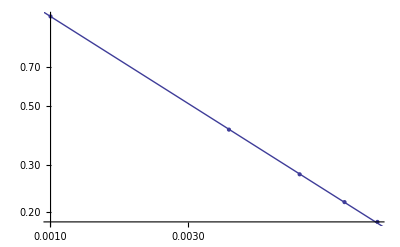

```mathematica
(*Test the fit. Note that the x-axis is now inverted and positive*)
Show[{ListLogLogPlot[{Abs[Take[Take[chiBlisth0TCEP,321],-5]]}],LogLogPlot[{model/.fit0TCEP},{m,0.0005,-(mum-muCEP)/muCEP},AxesOrigin->{0,Automatic}]}]
```

### Baryon number susceptibility on the cross over phase border line

```mathematica
step=200;
lineAngel[eps_]:=TCEP+Tan[alpha+eps] (mu-muCEP);
fitTcCrOlA=FindFit[Take[TCrOlistOth,-10],lineAngel[0],{alpha},mu];
TcCrOlA[mu_,eps_]=lineAngel[eps]/.fitTcCrOlA;
```

```mathematica
TCEP
TcCrOlA[muCEP,eps]
```

0.0418454

0.0418454

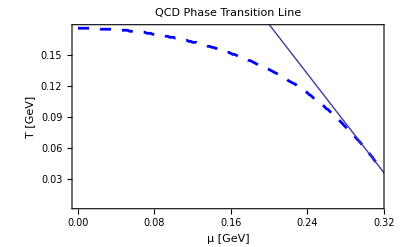

```mathematica
Show[plotCrossOverOth,Plot[TcCrOlA[mu,0],{mu,mum,mup}]]
```

```mathematica
(*Baryon number Susceptibility near the CEP for eps=h0 on the cross over phase border line*)
step=400;
mum1=muCEP(1-0.02);
mup1=muCEP(1+0.02);
ProgressBar[mu,mup1,mum1]
chiBlisth0Cro=Table[{(TcCrOlA[mu,0]-TCEP)/TCEP,chiB[eps0,TcCrOlA[mu,0],mu]},{mu,mum1,mup1,(mup1-mum1)/step}]//Quiet;
Export["chiBlisth0_Cro_esb.wdx",chiBlisth0Cro,"WDX"];
```

%

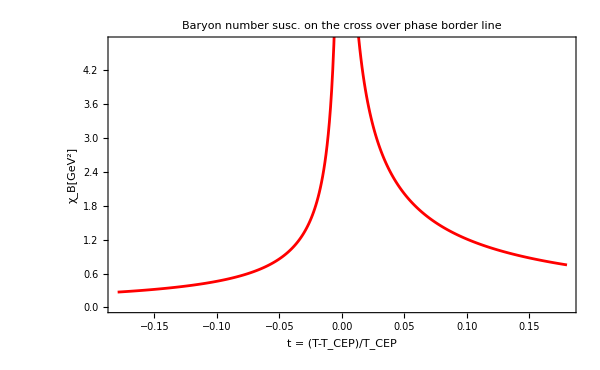

```mathematica
(*Plot the results*)
chiBlisth0Cro=Import["chiBlisth0_Cro_esb.wdx"];
plot=ListPlot[{Take[Re[chiBlisth0Cro],400]},FrameLabel->{"t = (T-T_CEP)/T_CEP","χ_B[GeV^2]"},LabelStyle->{FontSize->16},Joined->True,Frame->True,PlotLabel->Style["Baryon number susc. on the cross over phase border line",FontSize->18],ImageSize->{600,400},PlotRange->Automatic,PlotStyle->{Directive[Red,AbsoluteThickness[2]]},AxesOrigin->{-0.18,0}]
Export["chiBlisth0_Ta0_esb.pdf",plot,"PDF"];
```

```mathematica
(*Fit the susc. for t<0 to determine the scaling coefficient β*)
model=α t^(-β);
fit01st=FindFit[Abs[Take[Take[Re[chiBlisth0Cro],200],-5]],model,{α,β},t]
```

{α→0.323024,β→0.625598}

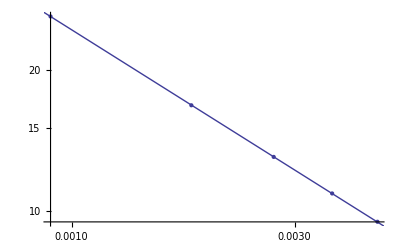

```mathematica
(*Test the fit. Note that the x-axis is now inverted and positive*)
Show[{ListLogLogPlot[{Abs[Take[Take[chiBlisth0Cro,200],-5]]}],LogLogPlot[{model/.fit01st},{t,0.0001,1}]}]
```

### All scaling coefficients at a clance (χ_B ~.1d t^-β, χ_B ~.1d m^-β )

```mathematica
(*all scaling coefficients at a glance*)
step=200;
tab2={{β/.fit0muCEP,β/.fit0TCEP,β/.fit01st}};
TableForm[tab2,TableHeadings->{{"ϵ=0"},{"μ=μ_CEP","T=T_CEP","T=T_(a = 0)"}}]
```

| μ=μ_CEP | T=T_CEP | T=T_(a = 0)
ϵ=0 | 0.694921 | 0.681363 | 0.625598